```mathematica
<< "/home/pablo/Escritorio/Uni/RRT/RandomData.m";
RandomData[]
RandomExp[100]
```

```mathematica
Histogram[Table[RandomData[],{30000}]]
```

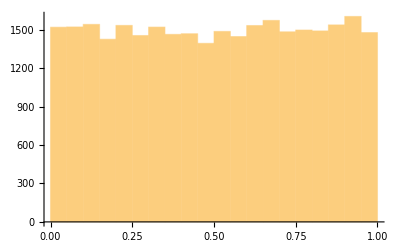

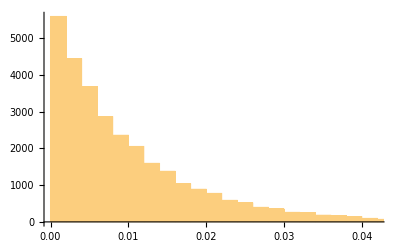

```mathematica
Histogram[Table[RandomExp[100],{30000}]]
```

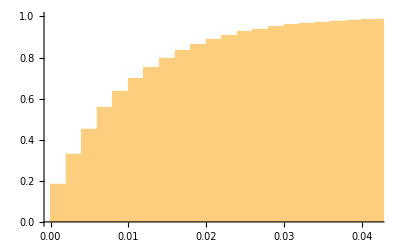

```mathematica
Histogram[Table[RandomExp[100],{30000}], 50,"CDF"]
```

```mathematica
FifoSchedulling[arrivals_,service_]:=Module[{n,checkTime},n=1;checkTime=arrivals[[1]];
(If[checkTime≥#,checkTime+=service[[n++]],checkTime=#+service[[n++]]])&/@arrivals]
```

```mathematica
nmax=100;
mu=200;
ro=0.8;
lambda=mu*ro;
InterArrivalsTime=Table[RandomExp[lambda],{nmax}];
ArrivalsTime=Accumulate[InterArrivalsTime];
ServiceTime=Table[RandomExp[mu],{nmax}];
DepartureTime=FifoSchedulling[ArrivalsTime, ServiceTime];
```

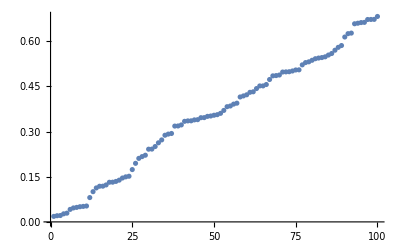

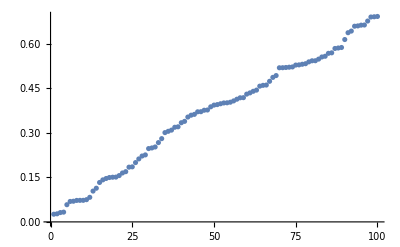

```mathematica
ListPlot[ArrivalsTime]
ListPlot[DepartureTime]
```